### Settings for 2D hydrogen problem; E = -1/[2*(n-1/2)^2]; each states are (2(n-1)+1) times degenerate Exact energies: E0 = -2Ha; E1 = -1/4.5 ~ -0.222 Ha;

```mathematica
delta = 0.0001;
rMax= 40;
```

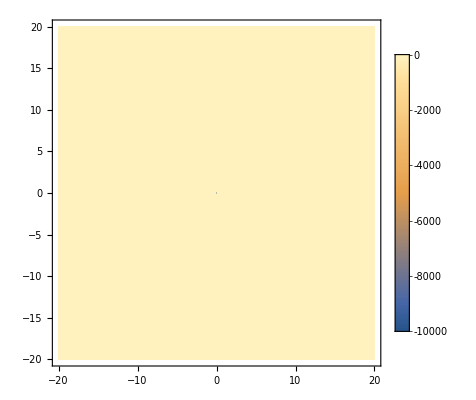

```mathematica
V[r_] := -1/(Abs[r] + delta) + 2; 
DensityPlot[V[r]/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y],{x,-rMax,rMax},{y,-rMax,rMax},(* PlotTheme->"Minimal", *)PlotPoints->100,  PlotLegends->Automatic, PlotRange->All]
```

### 2 D Problem

```mathematica
{egnVal,egnVec}=NDEigensystem[
{(-1/2)* Laplacian[R2D[r,θ],{r,θ},"Polar"]+V[r]*R2D[r,θ],
DirichletCondition[R2D[r,θ]==0,r==rMax*Sqrt[2]&&0<θ<=2*Pi],
PeriodicBoundaryCondition[R2D[r,θ],θ==0,TranslationTransform[{0,2 π}]]},
R2D[r,θ],{r,0,rMax*Sqrt[2]},{θ,0,2 π},10,Method->{"Eigensystem"->{"Arnoldi","MaxIterations"->100000} (*"Eigensystem" ->"Direct"*),"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}}} ];
ord =Ordering[egnVal];
Sort[Re[egnVal]]
```

{0.00734637,1.77781,1.77781,1.77804,1.92001,1.92001,1.92001,1.92001,1.92006,1.95968}

```mathematica
F1 =Part[Re[egnVec],Part[ord,1]]^2;
DensityPlot[F1/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y],{x,-2rMax,2rMax},{y,-2rMax,2rMax}, PlotTheme->"Minimal",  PlotPoints->100, PlotRange->All];
DensityPlot[F1/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y]+2π,{x,-2rMax,2rMax},{y,-2rMax,2rMax}, PlotTheme->"Minimal", PlotPoints->100,PlotRange->All (* PlotLegends->Automatic*)];
Show[{%,%%}]
Export[NotebookDirectory[]<>"1.png",%,ImageResolution->100];
```

```mathematica
str=OpenWrite[NotebookDirectory[]<>"data_1.dat", FormatType->StandardForm];
$Output={str};
Do[Print[x ,"  ",  F1/.r->x/.θ->0], {x, 0, rMax, 0.1 }];
Close[str];
```